# WEEK-3

1. Find the volume of the solid that is obtained when the region under the curve y = √x over the interval [1,4] is revolved about the x-axis.

```mathematica
V = π ∫_a^b [f(x)]^2 ⅆx ; x axis
```

```mathematica
f[x_] := √x;
```

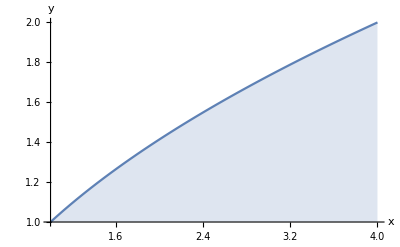

```mathematica
Plot[{f[x]},{x,1,4},PlotRange -> Automatic,PlotLegends ->"Expressions",AxesLabel -> {x,y}, Filling->Axis]
```

```mathematica
V = Pi * Integrate[(f[x])^2,{x,1,4}]
```

(15 π)/2

## 2. Volumes by slicing Washers:

```mathematica
V1 = π∫_a^b [f[x]^2-g[x]^2]ⅆx
```

Find the volume of the solid generated when the region between the graphs of the equations f(x) = 1/2 + x^2and g(x) over the interval [0,2] is revolved about the x-axis.

```mathematica
V = Pi * ∫_0^2 ((1/2+x^2)^2-(x)^2)ⅆx
```

(69 π)/10

3. Cylindrical shell

V = ∫_a^b 2πx[f(x)-g(x)]ⅆx; y axis

Use cylindrical shells to find the volume of the solid generated when the region enclosed between y = √x,x=1, x=4 and the x-axis is resolved about the y-axis.

```mathematica
V = 2 * π * ∫_1^4 x √x ⅆx
```

(124 π)/5

4. V = ∫_c^d 2πy[f(y)-g(y)]ⅆy; x axis

Use cylindrical shells to find the volume of the solid generated when the region enclosed between y^2=x, y=1, x=0 and the x-axis is resolved about the x-axis.

```mathematica
V = 2 * Pi * ∫_0^1 y*y^2 ⅆy
```

π/2